# Vaje 4

13. 3. 2025

## 1. kolokvij iz Matematike 1

1. Dokaži, da je za vsako naravno število  izraz  deljiv s .

```mathematica
izraz[n_] = Power[2, 2n+1]-9n^2 +3n -2
```

-2+2^(1+2 n)+3 n-9 n^2

```mathematica
(* Baza indukcije*)
izraz[0]
```

0

```mathematica
(* Indukcijski korak *)
```

```mathematica
izraz[n+1] - izraz[n] // FullSimplify
```

6 (-1+4^n-3 n)

```mathematica
izraz2[n_]:= -1+4^n-3n
```

```mathematica
izraz2[1]
```

0

```mathematica
(* korak *)
izraz2[n+1] - izraz2[n] // FullSimplify
```

3 (-1+4^n)

```mathematica
izraz3[n_]:=-1+4^n
```

```mathematica
izraz3[1]
```

3

```mathematica
izraz3[n+1]-izraz3[n] // FullSimplify
```

3 4^n

2.  Določi vsa realna števila , ki zadoščajo neenačbi .

```mathematica
Reduce[Abs[x^2+3x+2]+Abs[x+2] > 2x^2+x, x, Reals]
```

-1<x<4

3. V kompleksnih številih reši enačbo . Rešitve nariši v kompleksni ravnini.

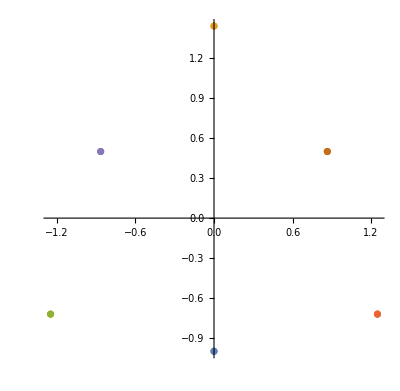

```mathematica
Solve[z^6+2I*z^3+3==0, {z}] // Values  // ComplexListPlot
```

4. Dana je množica . Ugotovi, katere od količin min A, inf A, max A in sup A obstajajo ter jih določi. Vse odgovore natančno utemelji.

```mathematica
A[n_]:=(8n+2)/(4n-1)
```

```mathematica
Limit[A[n], n-> Infinity]
```

2

```mathematica
Reduce[{A[n+1]-A[n] < 0, n > 0, Element[n, Integers]}, n]
```

n∈ℤ&&n≥1

```mathematica
Solve[A[n] == 2, n]
```

{}

```mathematica
(* 2 je infimum ni minimum*)

A[1]
```

10/3

```mathematica
(*max = sup = 10/3 *)
```

## 2. kolokvij iz Matematike 1

1. Funkcija  je podana s predpisom

 
Izračunaj naravno definicijsko območje funkcije  in izračunaj kompozitum , kjer je 

g funkcija, ki je za  enaka , sicer pa je enaka .

```mathematica
clear[izraz]
```

clear[izraz]

```mathematica
f[x_]:=Log[ArcSin[Divide[3+x, 3x-1]]]
```

```mathematica
g[x_]:= Piecewise[{
{E^x, x<=Log[Pi/2]},
{E^(-x), x>Log[Pi/2]}
}]
```

```mathematica
FunctionDomain[f[x], x]
```

x<-3||x≥2

```mathematica
g[f[x]] // FullSimplify
```

Piecewise[{{1/ArcSin[(3+x)/(-1+3 x)], Log[ArcSin[(3+x)/(-1+3 x)]]>Log[π/2]}, {ArcSin[(3+x)/(-1+3 x)], True}}]

2. Izračunaj naslednjo limito

.

```mathematica
Clear[izraz]
```

```mathematica
izraz[n_]:=Divide[n+2, Power[Factorial[n+1], 1/n]]
```

```mathematica
Limit[izraz[n], n->Infinity]
```

ⅇ

3. V odvisnosti od  preuči konvergenco zaporednja , ki je podano rekurzivno: , , kjer je  naravno število. V primerih ko zaporedje konvergira, zapiši še njegovo limito.

```mathematica
a[1]=x;
```

```mathematica
a[n_]:=Divide[(9-a[n-1])*a[n-1], 6];
Clear[f]

f[x_]:=Divide[(9-x)*x, 6]
```

```mathematica
Solve[x== f[x]]
```

{{x→0},{x→3}}

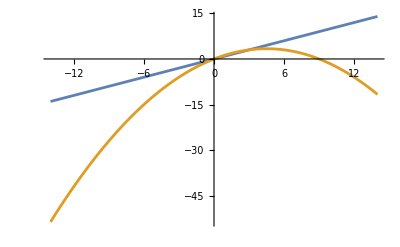

```mathematica
Plot[{x, f[x]}, {x, -14, 14}]
```

4. Poišči vsa realna števila , za katera konvergira vrsta 

.

```mathematica
Clear[f]
f[n_]:=Divide[Power[x, n], x^(2n)+n] (* Ce je x=0 je vsota vrste enaka 0*)
```

```mathematica
f[n+1]/f[n]// FullSimplify (* x != 0*)
```

```mathematica
(x (n+x^(2 n)))/(1+n+x^(2+2 n))
```

(x (n+x^(2 n)))/(1+n+x^(2+2 n))

```mathematica
Limit[f[n+1]/f[n],n->Infinity]
```

```mathematica
ConditionalExpression[1/x, x∈Reals&&Log[x]>0] (*Za x > 1 konvergira po kvoc. kriteriju*)
```

## 3. kolokvij iz Matematike 1

-Graphics-